```mathematica
ΔT = 10;  (* seconds *)
Subscript[ν, 0] = 10;  (* hertz *)
Subscript[ν, s] = {20, 21, 50, 100} ; (* sample frequencies *)
```

```mathematica
s[t_] := E^(-t/ΔT)Sin[2 Pi Subscript[ν, 0] t] HeavisideTheta[t]
```

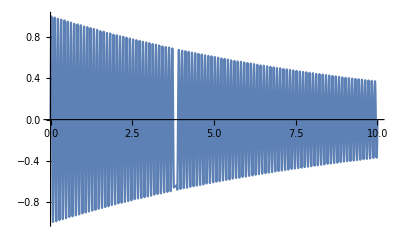

```mathematica
Plot[s[t], {t,0, 10}, PlotRange->Full]
```

```mathematica
FourierTransform[s[t],t,ω]
```

(1000 √(2 π))/(1+40000 π^2-20 ⅈ ω-100 ω^2)

```mathematica
(* SAMPLING AND RECONSTRUCTION *)
points = Range[0, 100, 1/Subscript[ν, s][[2]] ];
samples = Map[s, points];
Subscript[s, rec][t_, samples_, T_] := Sum[ samples[[n]] Sinc[Pi/T(t-n T)], {n, 1, Length@samples} ]
```

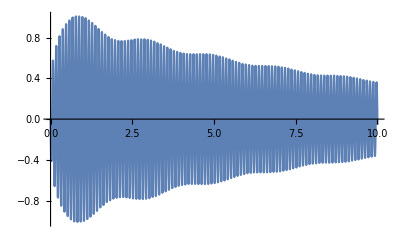

```mathematica
Plot[Subscript[s, rec][t, samples, 1/Subscript[ν, s][[2]]], {t, 0, 10}, PlotRange->Full]
```